```mathematica
<<KerrGeodesics`
<<SpinWeightedSpheroidalHarmonics`
```

```mathematica
a=.998`32;
r0 = 10`32;
x = Cos[π/4`32];
Freqs=KerrGeoFrequencies[a,r0,0,x];
Ωθ=Freqs[[2]];
Ωϕ= Freqs[[3]];
orbit = KerrGeoOrbit[a,r0,0,x];
{t,r,θ,ϕ} = orbit["Trajectory"];
Υ = orbit["Frequencies"]["Υ_θ"];
Υϕ = orbit["Frequencies"]["Υ_ϕ"];
ℰ=orbit["Energy"];
ℒ=orbit["AngularMomentum"];
```

```mathematica
l=3;
m=1;
k=3;
dtdλ[θ_]:= ℰ(((r0^2+a^2)^2)/(r0^2-2 r0+a^2)-a^2 Sin[θ]^2)+a ℒ(1-(r0^2+a^2)/(r0^2-2r0 +a^2))
ω = m Ωϕ + k Ωθ;

S = Table[SpinWeightedSpheroidalHarmonicS[0,l,m,a (m Ωϕ+k Ωθ)],{l,0,5},{m,-l,l},{k,-5,5}];
```

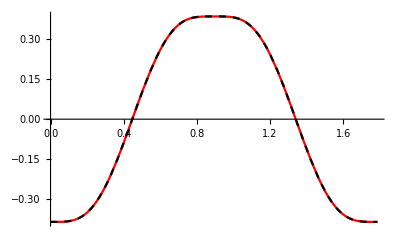

```mathematica
Plot[{S[[2+1,2+1+1,6+3]][θ[λ],0],SpinWeightedSpheroidalHarmonicS[0,2,1,a(1Ωϕ+ 3 Ωθ),θ[λ],0]},{λ,0,(2π)/Υ},PlotStyle->{Red,{Black,Dashed}}]
```

```mathematica
T = Table[NIntegrate[S[[l+1,l+m+1,6+k]][θ[λ],0]Cos[m(Ωϕ t[λ]-ϕ[λ])+k Ωθ t[λ]]dtdλ[λ],{λ,0,(2π)/Υ},Method->"Trapezoidal"],{l,0,5},{m,-l,l},{k,-5,5}];
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in λ in the region {{0.,1.78664}}. NIntegrate obtained 0.000365372 and 5.3314×10^-9 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in λ in the region {{0.,1.78664}}. NIntegrate obtained 0.000679965 and 5.33021×10^-9 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in λ in the region {{0.,1.78664}}. NIntegrate obtained 0.0010265 and 5.32928×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvi will be suppressed during this calculation.

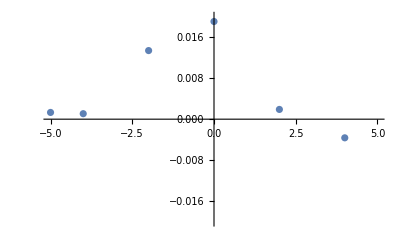

```mathematica
l=4;
m=-3;
ListPlot[Thread[{Table[k,{k,-5,5}],T[[l+1,l+m+1]]}],PlotRange->{-.02,.02}]
```

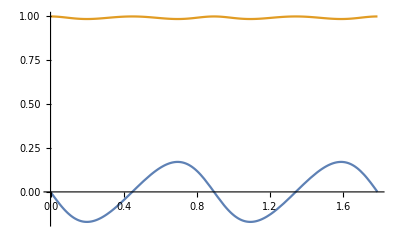

```mathematica
Plot[{m(Ωϕ t[λ]-ϕ[λ]),Cos[m(Ωϕ t[λ]-ϕ[λ])]},{λ,0,2 π/Υ}]
```

```mathematica
(Cos[A+B]//TrigExpand)/.{A->HoldForm [k Ωθ t[λ]],B-> HoldForm[m(Ωϕ t[λ]-ϕ[λ])]}
```

Cos[k Ωθ t[λ]] Cos[m (Ωϕ t[λ]-ϕ[λ])]-Sin[k Ωθ t[λ]] Sin[m (Ωϕ t[λ]-ϕ[λ])]

```mathematica
Plot[Cos[k Ωθ t[λ]] Cos[m (Ωϕ t[λ]-ϕ[λ])]-Sin[k Ωθ t[λ]] Sin[m (Ωϕ t[λ]-ϕ[λ])],{λ,0,(2π)/Υ}]
```

-Graphics-

```mathematica
HoldForm[S[θ[λ],0]Cos[m Ωϕ t[λ]-m ϕ[λ] + k Ωθ t[λ]]dtdλ[θ[λ]]]/.{λ->T-λ}
```

S[θ[T-λ],0] Cos[m Ωϕ t[T-λ]-m ϕ[T-λ]+k Ωθ t[T-λ]] dtdλ[θ[T-λ]]

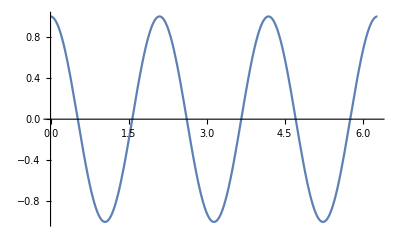

0

```mathematica
Plot[Cos[k t],{t,0,2π}]
Integrate[Cos[4 t],{t,0,2π}]
```

```mathematica
Plot[]
```

Plot::argrx: Plot called with 0 arguments; 2 arguments are expected.

Plot[]

```mathematica
ℒ
```

2.4798003304983163959845227696